```mathematica
SetDirectory[NotebookDirectory[]];
omega=Flatten[Import["./mub0T1/buffer/omega.dat"]];
re1=Flatten[Import["./mub0T1/buffer/Re.dat"]];
Im1=Flatten[Import["./mub0T1/buffer/Im.dat"]];
rho1=Transpose[{omega,-1/π*Im1/(re1^2+Im1^2)}];
omega=Flatten[Import["./mub0T100/buffer/omega.dat"]];
re100=Flatten[Import["./mub0T100/buffer/Re.dat"]]+Flatten[Import["./mub0T100/buffer/mrho2bare.dat"]];
Im100=Flatten[Import["./mub0T100/buffer/Im.dat"]];
rho100=Transpose[{omega,-1/π*Im100/(re100^2+Im100^2)}];
omega=Flatten[Import["./mub0T130/buffer/omega.dat"]];
re130=Flatten[Import["./mub0T130/buffer/Re.dat"]]+Flatten[Import["./mub0T130/buffer/mrho2bare.dat"]];
Im130=Flatten[Import["./mub0T130/buffer/Im.dat"]];
rho130=Transpose[{omega,-1/π*Im130/(re130^2+Im130^2)}];
omega=Flatten[Import["./mub0T150/buffer/omega.dat"]];
re150=Flatten[Import["./mub0T150/buffer/Re.dat"]]+Flatten[Import["./mub0T150/buffer/mrho2bare.dat"]];
Im150=Flatten[Import["./mub0T150/buffer/Im.dat"]];
rho150=Transpose[{omega,-1/π*Im150/(re150^2+Im150^2)}];
omega=Flatten[Import["./mub0T160/buffer/omega.dat"]];
re160=Flatten[Import["./mub0T160/buffer/Re.dat"]]+Flatten[Import["./mub0T160/buffer/mrho2bare.dat"]];
Im160=Flatten[Import["./mub0T160/buffer/Im.dat"]];
rho160=Transpose[{omega,-1/π*Im160/(re160^2+Im160^2)}];
omega=Flatten[Import["./mub0T200/buffer/omega.dat"]];
re200=Flatten[Import["./mub0T200/buffer/Re.dat"]]+Flatten[Import["./mub0T200/buffer/mrho2bare.dat"]];
Im200=Flatten[Import["./mub0T200/buffer/Im.dat"]];
rho200=Transpose[{omega,-1/π*Im200/(re200^2+Im200^2)}];
```

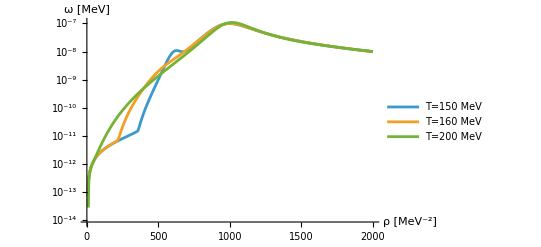

```mathematica
plot1=ListLinePlot[{rho150,rho160,rho200},ScalingFunctions->"Log",PlotLegends->{(*"T=1 MeV","T=100 MeV","T=130 MeV",*)"T=150 MeV","T=160 MeV","T=200 MeV"},AxesLabel->{"ρ [MeV^-2]","ω [MeV]"}]
```

```mathematica
Export["./rho.pdf",plot1]
```

./rho.pdf